```mathematica
Clear["Global`*"]

series=Series[Tanh[β(h+J n m)],{h,hbar,10}];
coeffs=CoefficientList[Normal[series]/. (h-hbar)->σ,σ];
evenMomentExpansion=Table[
With[{coeff=coeffs[[k+1]],order=k},
If[k==0,
coeff &,
coeff #^order(order-1)!! &
]
],
{k,0,Length[coeffs],2} ];

findSolutionRobust[equation_,startingPoint_,hbarVal_]:=Module[{solution},solution=Quiet@Check[FindRoot[equation,{m,startingPoint},AccuracyGoal->6,PrecisionGoal->6,MaxIterations->100],
$Failed];
If[solution=!=$Failed,
m/.solution,
Sow[hbarVal,"failed"];
Missing["FindRootFailed"]
]
];
```

Default variables

```mathematica
β=1; (*inverse temp*)
J=2; (*coupling*)
n=1; (*number of spins*)
hbarValues=Range[-1.0,1.0,0.01];
```

#### Magnetization using n^th order approximation

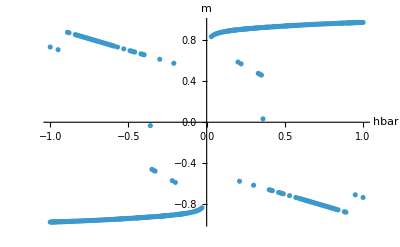

```mathematica
maxMoment=10;(*must be even*)
σ=.9;

{mstarPositive,failedCollected}=Reap[
Table[
findSolutionRobust[m==Total[Table[evenMomentExpansion[[i]][σ],{i,1,maxMoment/2+1}]],π/2,hbar],
{hbar,hbarValues}
],
"failed"];
failedhbarPositive=If[
Length[failedCollected]>0,
failedCollected[[1]],
{}];

{mstarNegative,failedCollected}=Reap[
Table[
findSolutionRobust[m==Total[Table[evenMomentExpansion[[i]][σ],{i,1,maxMoment/2+1}]],-π/2,hbar],
{hbar,hbarValues}
],
"failed"];
failedhbarNegative=If[Length[failedCollected]>0,failedCollected[[1]],{}];

p1=ListPlot[Transpose[{hbarValues,mstarPositive}],
AxesLabel->{"hbar","m"}];
p2=ListPlot[Transpose[{hbarValues,mstarNegative}],
AxesLabel->{"hbar","m"}];
Show[{p1,p2}]
```

```mathematica
failedhbarNegative
```

{-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.85}